

```mathematica
Graph[{1<->2,2<->3,3<->1}]
```



```mathematica
Graph[{1->2,2->3,3->1}]
```

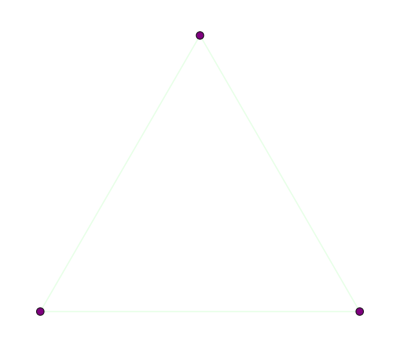

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexStyle->Purple,EdgeStyle->LightGreen]
```

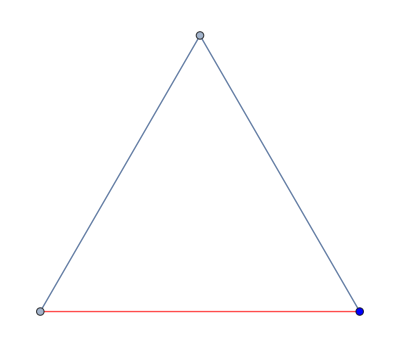

```mathematica
Graph[{1,2,Style[3,Blue]},{1<->2,2<->3,Style[3<->1,Red]}]
```

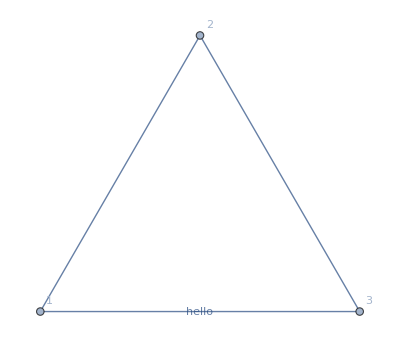

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->1,"hello"]},VertexLabels->"Name"]
```

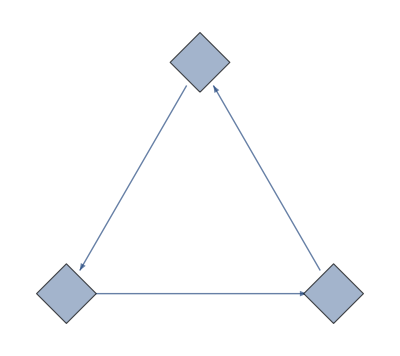

```mathematica
Graph[{1->2,2->3,3->1},VertexShapeFunction->"Diamond",VertexSize->Medium]
```

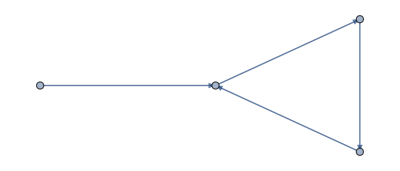

```mathematica
Graph[{1<->2,2->3,3->4,4->2},EdgeShapeFunction->"CarvedArcArrow"]
```

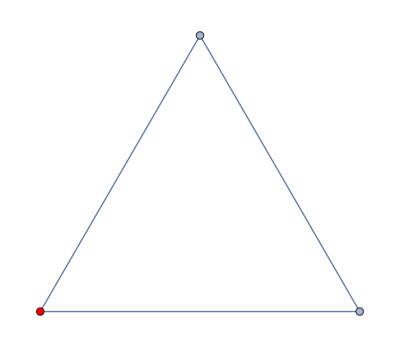
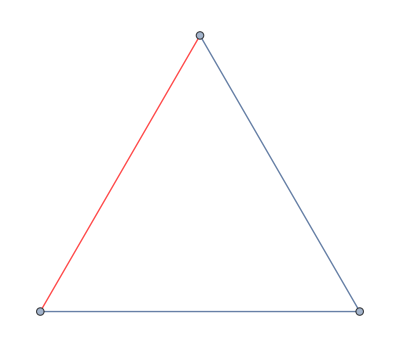

```mathematica
{Graph[{Style[1,Red],2,3},{1<->2,2<->3,3<->1}],Graph[{1,2,3},{Style[1<->2,Red],2<->3,3<->1}]}
```

Wrappers can be nested:

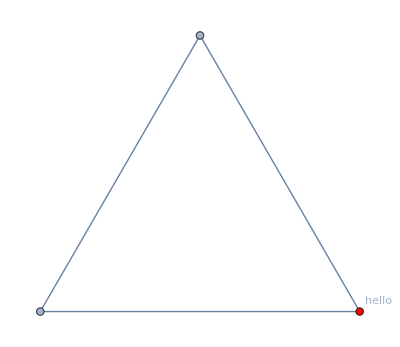
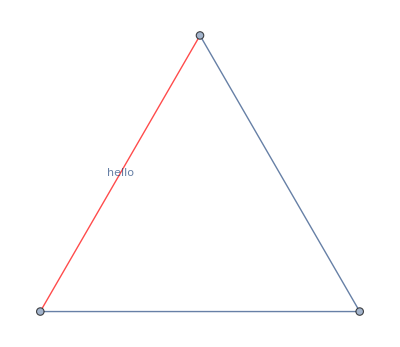

```mathematica
{Graph[{1,2,Labeled[Style[3,Red],"hello"]},{1<->2,2<->3,3<->1}],Graph[{1,2,3},{Style[Labeled[1<->2,"hello"],Red],2<->3,3<->1}]}
```

Add interactive behavior by wrappers such as Tooltip:

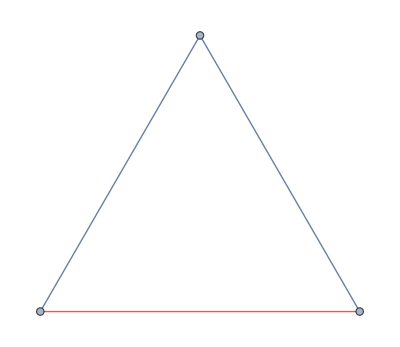

```mathematica
Graph[{1<->2,2<->3,Tooltip[Style[3<->1,Red],"hello"]}]
```

Any object can be used in the tooltip:

```mathematica
Graph[{1<->2,2<->3,Tooltip[Style[3<->1,Red],Plot[Sin[x],{x,0,2π}]]}]
```

-Graphics-

```mathematica
Graph[{1<->2,2<->3,Tooltip[Style[3<->1,Red],RandomGraph[BarabasiAlbertGraphDistribution[40,3]]]}]
```

-Graphics-

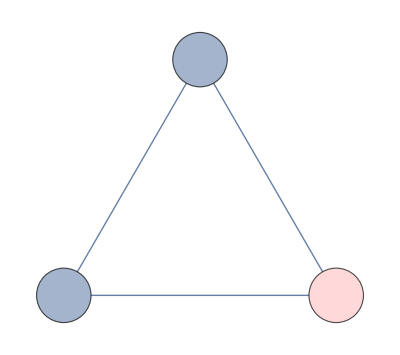
{-Graphics-,-Graphics-}

```mathematica
{Graph[{1<->2,2<->3,Button[Style[3<->1,Red],Speak["Undirected edge from node 3 to node 1"]]}],Graph[{1,2,Button[Style[3,LightRed],Speak["Node/Vertex 3"]]},{1<->2,2<->3,3<->1},VertexSize->Medium]}
```

```mathematica
Graph[{UndirectedEdge[a,b],UndirectedEdge[b,c],UndirectedEdge[c,a]}]
```

-Graphics-

```mathematica
EdgeList[Graph[{a, b, c}, {UndirectedEdge[a, b], UndirectedEdge[b, c], UndirectedEdge[c, a]}]]
```

{a<->b,b<->c,c<->a}

```mathematica
Graph[{DirectedEdge[a,b],DirectedEdge[b,c],DirectedEdge[c,a]}]
```

-Graphics-

```mathematica
DirectedEdge[a,b,d]
```

abd

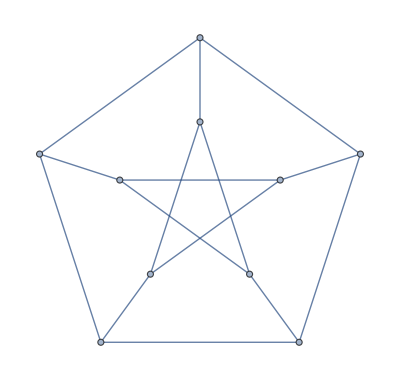

```mathematica
PetersenGraph[]
```

```mathematica
VertexList[PetersenGraph[]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
VertexList[PetersenGraph[],_?(#>2&)]
```

{3,4,5,6,7,8,9,10}

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

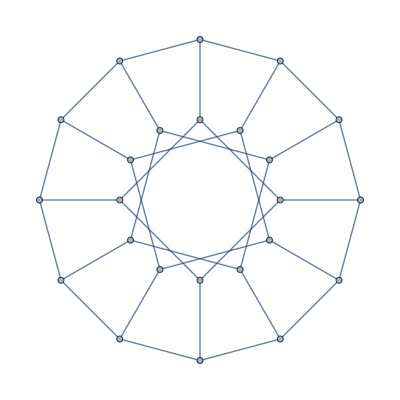

```mathematica
PetersenGraph[12,3]
```

```mathematica
VertexList[PetersenGraph[12,3]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

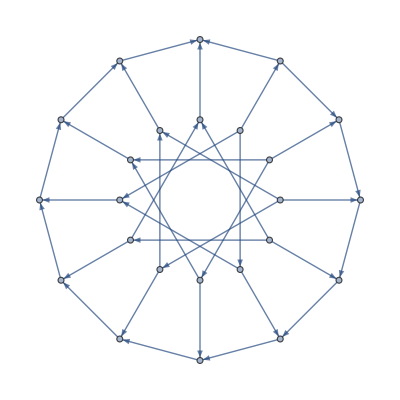

```mathematica
UndirectedGraphToMixedGraph[PetersenGraph[12,4],1]
```

```mathematica
VertexList[UndirectedGraphToMixedGraph[PetersenGraph[12,4],1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
EdgeList[PetersenGraph[]]
```

{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10}

```mathematica
EdgeList[PetersenGraph[],1<->_]
```

{1<->3,1<->4,1<->6}

```mathematica
EdgeList[RandomMixedGraph[{20,54},0.5],_<->_]
```

{1<->4,1<->7,1<->18,2<->8,3<->12,3<->16,4<->11,4<->13,5<->8,5<->17,5<->19,6<->7,6<->10,6<->14,6<->20,7<->8,7<->12,7<->20,8<->9,8<->16,8<->17,8<->19,10<->13,10<->17,13<->14,13<->19,15<->20}

```mathematica
EdgeList[RandomMixedGraph[BarabasiAlbertGraphDistribution[1000,2],0.5],_<->_]//RepeatedTiming
```

{2.30195,{1<->2,1<->9,1<->32,1<->371,1<->381,1<->464,1<->502,1<->892,2<->4,2<->59,2<->165,2<->442,2<->487,2<->501,2<->528,2<->655,2<->656,2<->737,2<->857,3<->5,3<->38,3<->45,3<->46,3<->114,3<->136,3<->148,3<->215,3<->218,3<->247,3<->329,3<->353,3<->416,3<->593,3<->600,3<->604,3<->646,3<->788,3<->796,3<->808,3<->961,4<->6,4<->7,4<->10,4<->13,4<->20,4<->22,4<->28,4<->29,4<->41,4<->52,4<->60,4<->64,4<->77,4<->89,4<->133,4<->138,4<->148,4<->189,4<->240,4<->241,4<->277,4<->319,4<->347,4<->588,4<->617,4<->634,4<->667,4<->683,4<->697,4<->698,4<->745,4<->818,5<->8,5<->18,5<->23,5<->27,5<->53,5<->105,5<->115,5<->134,5<->135,5<->194,5<->289,5<->292,5<->411,5<->607,5<->773,5<->783,5<->837,6<->206,6<->298,6<->477,6<->526,6<->810,7<->44,7<->49,7<->57,7<->88,7<->202,7<->235,7<->293,7<->319,7<->330,7<->365,7<->366,7<->402,7<->417,7<->501,7<->525,7<->555,7<->577,7<->638,7<->690,7<->819,7<->863,7<->878,7<->918,7<->951,8<->106,8<->223,8<->751,9<->13,9<->19,9<->137,9<->157,9<->200,9<->398,9<->600,10<->11,10<->14,10<->25,10<->68,10<->124,10<->151,10<->156,10<->209,10<->341,10<->588,10<->699,10<->700,10<->768,10<->792,10<->945,11<->17,11<->23,11<->33,11<->55,11<->60,11<->146,11<->166,11<->213,11<->215,11<->230,11<->268,11<->378,11<->585,11<->729,11<->842,11<->985,12<->199,12<->338,12<->616,12<->807,13<->31,13<->427,13<->685,13<->735,13<->768,13<->812,13<->980,14<->22,14<->42,14<->48,14<->88,14<->269,14<->336,14<->457,14<->557,14<->591,14<->715,14<->720,14<->749,14<->785,16<->18,16<->20,16<->240,16<->416,16<->476,16<->530,16<->702,16<->783,16<->891,17<->37,17<->73,17<->78,17<->81,17<->181,17<->188,17<->373,17<->385,17<->456,17<->523,17<->619,17<->966,17<->977,18<->34,18<->167,18<->168,18<->304,18<->345,18<->351,19<->36,19<->46,19<->56,19<->74,19<->82,19<->108,19<->127,19<->129,19<->134,19<->140,19<->154,19<->231,19<->239,19<->272,19<->403,19<->446,19<->488,19<->507,19<->601,19<->914,20<->367,20<->610,20<->611,21<->51,21<->99,21<->156,21<->580,21<->866,22<->24,22<->143,22<->322,22<->356,22<->400,22<->500,22<->963,23<->67,23<->81,23<->180,23<->301,23<->308,23<->342,23<->459,23<->721,24<->32,24<->82,24<->133,24<->463,24<->719,24<->926,25<->54,25<->62,25<->316,25<->428,25<->629,25<->769,26<->33,26<->112,26<->113,26<->128,26<->364,26<->520,26<->534,26<->562,26<->756,27<->43,27<->151,27<->337,27<->435,27<->436,27<->514,27<->610,28<->73,28<->327,30<->155,30<->795,31<->386,31<->997,32<->116,32<->145,32<->315,32<->469,32<->516,32<->572,32<->957,33<->57,33<->355,34<->278,34<->417,34<->510,34<->571,34<->572,34<->655,34<->660,34<->665,34<->839,35<->63,36<->56,36<->110,36<->222,36<->681,36<->879,36<->958,36<->960,38<->89,38<->141,38<->162,38<->207,38<->283,38<->630,39<->111,40<->42,40<->138,40<->176,40<->475,40<->511,40<->545,40<->620,40<->985,41<->58,41<->61,41<->112,41<->197,41<->287,41<->712,41<->716,42<->59,42<->251,42<->555,42<->931,43<->48,43<->574,44<->71,44<->100,44<->190,44<->218,44<->248,44<->295,44<->343,44<->413,44<->537,44<->589,44<->613,44<->782,44<->798,44<->846,45<->87,45<->118,45<->186,45<->363,45<->561,45<->589,45<->707,45<->749,45<->832,45<->858,46<->676,46<->816,47<->116,47<->145,47<->171,47<->204,47<->243,47<->260,47<->305,47<->521,47<->611,47<->642,47<->664,47<->668,47<->670,47<->744,47<->746,47<->922,47<->954,48<->50,48<->77,48<->119,48<->183,48<->220,48<->280,48<->321,48<->370,48<->384,48<->431,48<->505,48<->552,48<->954,48<->955,49<->254,50<->357,51<->66,52<->71,52<->237,52<->256,52<->273,52<->396,52<->517,52<->620,52<->811,52<->827,53<->102,53<->172,53<->294,54<->357,55<->76,57<->86,57<->103,57<->229,57<->245,57<->637,57<->801,57<->841,58<->114,58<->447,58<->631,58<->761,59<->605,62<->253,62<->306,63<->540,64<->469,65<->201,65<->622,66<->129,66<->179,66<->765,66<->815,66<->935,68<->96,68<->141,68<->338,68<->984,70<->349,70<->354,70<->405,70<->733,70<->819,71<->772,72<->346,72<->809,74<->84,75<->254,75<->519,75<->614,76<->181,76<->525,76<->559,76<->563,76<->741,77<->159,79<->436,80<->414,80<->732,81<->100,81<->166,81<->680,82<->83,83<->93,83<->261,83<->942,84<->391,85<->339,86<->238,86<->753,86<->808,87<->131,87<->147,87<->377,87<->450,87<->477,87<->625,88<->164,88<->361,88<->386,88<->632,88<->640,89<->191,89<->340,89<->432,89<->742,89<->853,90<->382,90<->466,90<->915,91<->227,93<->483,93<->629,95<->657,97<->98,97<->635,97<->763,97<->998,98<->504,98<->895,98<->968,99<->306,100<->452,101<->225,101<->230,101<->526,105<->330,105<->647,106<->127,106<->204,106<->673,110<->349,110<->899,110<->918,111<->710,112<->117,112<->259,112<->455,112<->509,112<->516,113<->236,113<->933,114<->593,115<->171,116<->602,117<->499,117<->518,117<->843,118<->636,118<->704,119<->170,120<->216,121<->393,123<->195,123<->530,123<->564,123<->681,123<->883,124<->205,124<->832,125<->154,125<->290,125<->448,125<->920,126<->170,126<->178,126<->287,126<->791,126<->795,126<->936,127<->274,130<->168,130<->291,130<->671,130<->889,131<->840,132<->265,132<->369,132<->894,134<->974,136<->219,136<->658,137<->235,137<->627,138<->522,140<->201,140<->540,140<->725,140<->747,141<->169,141<->942,143<->184,143<->185,143<->193,143<->203,143<->341,143<->543,143<->561,143<->969,143<->990,145<->305,145<->489,146<->903,147<->234,147<->325,150<->203,150<->328,150<->485,150<->579,151<->219,151<->282,151<->456,151<->527,152<->645,152<->762,153<->412,153<->934,154<->309,154<->389,155<->216,155<->266,155<->296,155<->481,155<->543,155<->583,155<->659,155<->979,156<->830,158<->515,159<->347,160<->510,162<->249,163<->242,164<->173,166<->404,167<->746,168<->626,172<->736,173<->423,173<->458,174<->565,174<->868,174<->901,175<->199,175<->231,175<->280,175<->302,175<->385,175<->523,175<->651,176<->550,177<->397,177<->420,179<->461,180<->669,180<->826,180<->857,181<->266,181<->862,181<->873,183<->893,184<->858,186<->595,186<->835,187<->685,187<->724,187<->848,188<->791,188<->865,190<->902,191<->265,191<->418,192<->206,192<->252,192<->558,192<->916,193<->196,193<->323,193<->712,193<->794,196<->250,196<->256,196<->364,196<->474,197<->247,197<->512,197<->608,198<->403,199<->298,199<->804,200<->290,200<->535,200<->941,201<->871,203<->307,203<->333,203<->538,204<->905,205<->715,206<->727,208<->989,209<->271,209<->524,209<->964,211<->590,211<->684,211<->758,211<->789,211<->803,213<->921,213<->943,217<->258,217<->362,217<->895,217<->994,218<->390,219<->890,219<->998,220<->363,220<->448,221<->260,221<->415,222<->616,223<->229,223<->856,224<->785,225<->441,225<->446,225<->983,226<->541,228<->754,230<->592,230<->828,230<->941,230<->944,232<->334,232<->738,233<->943,235<->677,237<->336,237<->576,237<->848,239<->634,241<->919,244<->726,245<->342,246<->675,252<->571,256<->775,256<->836,259<->270,259<->294,259<->299,259<->518,260<->302,260<->332,260<->851,262<->582,263<->344,263<->479,263<->723,264<->312,264<->313,264<->549,265<->307,266<->590,268<->421,269<->274,269<->285,269<->318,269<->862,270<->279,270<->950,271<->286,275<->281,276<->604,276<->821,278<->424,278<->692,278<->805,280<->936,282<->425,283<->318,284<->570,285<->359,286<->460,287<->711,288<->350,288<->377,288<->557,289<->465,289<->597,291<->568,291<->810,292<->414,292<->598,293<->407,293<->514,295<->409,296<->956,297<->492,297<->493,297<->619,301<->329,301<->924,303<->1000,310<->340,314<->375,319<->586,322<->419,326<->457,326<->915,327<->825,331<->367,331<->379,331<->581,332<->370,333<->649,333<->706,333<->908,333<->974,334<->624,334<->770,334<->842,334<->986,336<->353,336<->464,336<->503,336<->563,336<->659,336<->679,338<->493,340<->568,341<->505,346<->630,348<->379,348<->507,348<->978,350<->503,350<->850,356<->441,358<->462,358<->724,361<->969,362<->506,363<->508,365<->719,369<->752,369<->982,372<->400,372<->548,372<->758,374<->765,376<->1000,379<->381,379<->898,382<->755,383<->877,384<->427,385<->396,385<->965,386<->859,386<->962,387<->405,390<->490,393<->559,394<->397,394<->585,395<->406,396<->434,396<->470,397<->801,399<->558,399<->995,403<->430,403<->878,407<->612,410<->527,410<->717,411<->704,411<->750,411<->940,412<->920,420<->651,420<->689,421<->822,423<->796,424<->595,424<->881,427<->646,428<->471,428<->823,429<->891,430<->972,431<->635,432<->497,433<->814,442<->702,443<->468,443<->488,443<->627,444<->730,448<->688,449<->743,454<->771,458<->508,458<->722,460<->972,462<->547,462<->871,466<->554,473<->806,477<->718,481<->820,481<->833,483<->529,484<->650,484<->922,488<->575,488<->723,490<->777,490<->932,492<->929,493<->498,493<->695,497<->528,499<->948,501<->549,504<->773,506<->560,511<->607,519<->615,520<->854,521<->553,521<->938,523<->963,525<->956,526<->657,529<->603,532<->946,538<->544,549<->578,551<->983,554<->569,555<->762,558<->727,560<->615,568<->946,577<->628,577<->901,579<->731,582<->674,582<->703,587<->898,595<->731,597<->875,597<->976,607<->687,607<->933,609<->793,616<->756,616<->855,622<->927,625<->826,625<->935,626<->761,626<->821,629<->902,629<->908,633<->662,633<->812,633<->890,636<->944,638<->692,641<->852,643<->709,644<->693,657<->707,658<->872,672<->825,675<->693,675<->987,684<->851,701<->938,704<->831,706<->770,712<->887,725<->988,727<->806,733<->924,734<->991,736<->951,742<->759,742<->767,746<->769,761<->784,774<->934,777<->850,791<->805,798<->947,807<->996,835<->884,835<->959,837<->849,844<->919,844<->984,862<->873,870<->996,875<->894,889<->991,898<->999,903<->923,915<->957,922<->948}}

```mathematica
Cases[EdgeList[RandomMixedGraph[BarabasiAlbertGraphDistribution[1000,2],0.5]],_UndirectedEdge]//RepeatedTiming
```

{2.77134,{1<->3,1<->7,1<->9,1<->10,1<->15,1<->62,1<->70,1<->85,1<->107,1<->126,1<->147,1<->349,1<->376,1<->384,1<->404,1<->434,1<->449,1<->494,1<->513,1<->578,1<->610,1<->627,1<->647,1<->660,1<->725,2<->17,2<->21,2<->24,2<->37,2<->56,2<->78,2<->110,2<->188,2<->189,2<->195,2<->239,2<->248,2<->287,2<->288,2<->310,2<->363,2<->431,2<->443,2<->530,2<->554,2<->676,2<->691,2<->770,2<->796,2<->800,2<->908,3<->25,3<->44,3<->47,3<->54,3<->56,3<->60,3<->63,3<->81,3<->110,3<->122,3<->156,3<->178,3<->191,3<->236,3<->346,3<->385,3<->399,3<->513,3<->616,3<->682,3<->749,3<->756,3<->915,4<->8,4<->210,4<->286,4<->314,4<->398,4<->491,4<->764,4<->895,5<->7,5<->12,5<->27,5<->33,5<->36,5<->43,5<->64,5<->74,5<->79,5<->84,5<->139,5<->148,5<->289,5<->315,5<->322,5<->376,5<->409,5<->446,5<->453,5<->594,5<->603,5<->632,5<->639,5<->640,5<->667,5<->865,6<->49,6<->88,6<->186,6<->208,6<->223,6<->229,6<->254,6<->295,6<->426,6<->455,6<->538,6<->624,6<->663,6<->675,6<->688,6<->739,6<->887,7<->321,8<->15,8<->55,8<->94,8<->114,8<->129,8<->183,8<->185,8<->245,8<->607,8<->809,8<->824,8<->859,8<->890,9<->42,9<->95,9<->122,9<->129,9<->162,9<->273,9<->308,9<->328,9<->362,9<->381,9<->656,9<->693,9<->741,9<->743,9<->757,9<->818,9<->905,10<->13,10<->16,10<->38,10<->76,10<->77,10<->93,10<->112,10<->150,10<->156,10<->199,10<->207,10<->212,10<->219,10<->230,10<->238,10<->308,10<->343,10<->350,10<->358,10<->368,10<->583,10<->631,10<->633,10<->782,10<->845,10<->864,10<->921,10<->962,10<->986,11<->13,11<->123,11<->138,11<->207,11<->303,11<->329,11<->506,11<->830,12<->40,12<->41,12<->54,12<->85,12<->89,12<->97,12<->157,12<->173,12<->729,12<->981,13<->29,13<->39,13<->46,13<->61,13<->68,13<->119,13<->133,13<->172,13<->260,13<->263,13<->264,13<->449,13<->592,13<->625,13<->628,13<->677,13<->761,13<->763,13<->800,13<->910,13<->916,14<->32,14<->774,15<->19,15<->42,15<->82,15<->131,15<->206,15<->259,15<->274,15<->292,15<->470,15<->586,15<->671,15<->745,16<->144,16<->571,16<->670,16<->734,16<->948,17<->141,18<->49,18<->148,18<->174,18<->241,18<->262,18<->289,18<->406,18<->412,18<->438,18<->823,19<->240,19<->467,21<->393,21<->483,21<->642,21<->891,22<->113,22<->131,22<->177,22<->209,22<->522,22<->532,22<->542,22<->619,22<->681,22<->724,23<->83,23<->134,23<->380,23<->413,23<->471,23<->487,23<->643,23<->781,24<->177,24<->211,24<->307,24<->318,24<->400,24<->652,24<->711,24<->981,25<->104,25<->433,25<->454,25<->955,26<->792,26<->970,27<->31,27<->32,27<->72,27<->132,27<->154,27<->462,27<->489,27<->652,27<->722,27<->1000,28<->902,29<->158,29<->237,29<->267,29<->514,30<->181,30<->780,30<->949,31<->91,31<->543,31<->864,33<->45,33<->135,33<->509,33<->702,34<->275,34<->825,35<->70,35<->71,35<->103,35<->213,35<->520,35<->801,35<->880,36<->115,36<->244,36<->249,36<->414,36<->685,36<->718,37<->68,37<->141,37<->252,37<->439,37<->469,37<->730,38<->136,38<->211,38<->915,39<->51,39<->190,39<->298,39<->325,39<->327,39<->412,39<->750,40<->65,40<->142,40<->227,41<->339,42<->205,42<->215,42<->611,43<->153,43<->242,43<->261,43<->340,43<->435,43<->659,43<->809,44<->48,44<->74,44<->140,44<->149,44<->166,44<->176,44<->184,44<->195,44<->246,44<->250,44<->254,44<->273,44<->276,44<->330,44<->378,44<->386,44<->399,44<->561,44<->738,45<->109,45<->361,45<->396,45<->404,45<->451,45<->465,46<->90,46<->160,46<->200,46<->334,46<->407,46<->539,47<->53,47<->115,48<->362,48<->541,48<->798,49<->155,49<->179,49<->187,49<->232,49<->313,49<->320,50<->607,50<->695,50<->853,51<->170,51<->686,52<->258,52<->765,55<->268,56<->65,56<->120,56<->196,56<->575,56<->592,56<->831,57<->437,58<->87,58<->238,58<->354,58<->841,58<->918,59<->565,59<->977,60<->103,60<->206,60<->307,60<->355,60<->580,60<->624,60<->672,60<->974,61<->297,61<->441,61<->705,61<->767,63<->64,63<->318,63<->419,63<->544,63<->789,64<->127,64<->292,64<->757,64<->954,65<->351,65<->602,66<->155,66<->369,66<->498,66<->942,68<->648,69<->410,69<->510,70<->81,70<->306,71<->769,72<->234,74<->464,74<->635,74<->833,74<->931,75<->169,75<->247,75<->383,76<->585,77<->161,77<->167,77<->284,77<->527,77<->748,77<->771,77<->934,78<->364,78<->761,78<->914,79<->253,79<->268,79<->313,79<->510,79<->747,79<->781,80<->323,80<->331,80<->703,81<->163,81<->271,81<->395,82<->101,82<->168,82<->301,82<->417,82<->797,82<->811,82<->834,82<->837,83<->91,83<->448,85<->353,85<->552,86<->208,86<->317,86<->473,86<->889,86<->937,88<->814,89<->335,89<->988,90<->119,90<->325,90<->548,90<->621,91<->198,91<->224,91<->225,91<->290,91<->317,97<->427,98<->283,98<->360,98<->403,99<->255,100<->720,100<->943,101<->128,101<->367,101<->553,101<->609,101<->972,102<->113,102<->117,102<->257,102<->455,102<->564,102<->689,105<->108,105<->658,105<->768,106<->158,106<->199,106<->250,106<->280,106<->486,106<->597,106<->710,106<->866,106<->867,106<->935,112<->537,112<->641,113<->114,113<->371,113<->660,113<->894,113<->916,114<->972,115<->178,115<->402,116<->231,117<->180,117<->310,117<->451,117<->541,118<->182,118<->202,118<->256,119<->235,119<->301,119<->876,120<->366,121<->579,122<->303,122<->956,123<->381,123<->901,124<->145,124<->334,124<->622,124<->700,124<->743,124<->803,126<->200,126<->281,126<->802,127<->713,128<->137,128<->321,128<->649,128<->716,131<->776,132<->327,133<->217,133<->445,135<->197,135<->848,136<->515,137<->283,139<->350,140<->401,140<->748,140<->799,141<->324,142<->191,143<->185,143<->518,143<->655,143<->871,145<->429,146<->161,146<->394,146<->544,146<->638,148<->203,148<->213,149<->763,150<->373,150<->755,151<->239,152<->285,152<->881,153<->245,154<->209,154<->731,154<->895,154<->982,155<->479,157<->212,158<->616,160<->943,163<->302,164<->601,165<->796,167<->188,167<->257,167<->338,167<->546,167<->567,167<->568,172<->396,174<->304,177<->603,177<->724,177<->875,178<->198,178<->463,179<->480,180<->738,182<->596,182<->835,183<->204,183<->228,183<->241,184<->524,184<->687,184<->985,186<->262,187<->370,187<->545,187<->654,187<->708,188<->368,188<->617,188<->769,188<->885,193<->576,194<->897,195<->438,196<->281,196<->339,197<->534,198<->282,198<->542,200<->358,200<->664,201<->333,201<->487,202<->585,203<->356,204<->430,204<->634,206<->216,206<->595,207<->326,207<->919,209<->392,210<->423,210<->530,210<->537,210<->733,210<->804,210<->985,212<->681,212<->928,213<->994,214<->293,215<->296,215<->309,215<->357,215<->598,215<->631,216<->505,217<->401,218<->240,218<->469,220<->610,220<->968,222<->941,226<->562,226<->633,227<->299,227<->427,227<->870,229<->265,229<->702,229<->882,229<->888,231<->491,231<->935,234<->817,236<->835,238<->641,238<->789,239<->856,240<->345,240<->383,240<->766,241<->566,242<->397,243<->276,243<->360,243<->508,243<->574,247<->422,248<->387,249<->619,251<->716,252<->312,252<->911,253<->600,254<->405,255<->385,258<->305,258<->484,258<->857,259<->698,259<->850,260<->869,260<->955,262<->494,263<->570,263<->773,263<->858,263<->950,265<->852,268<->975,269<->902,270<->938,272<->768,273<->656,274<->479,276<->345,276<->749,278<->495,278<->785,279<->520,279<->701,280<->838,282<->754,285<->371,286<->815,289<->364,289<->551,290<->316,290<->574,290<->623,290<->872,294<->343,294<->655,294<->936,295<->355,295<->555,296<->417,296<->756,296<->946,299<->795,300<->588,300<->922,300<->977,302<->473,302<->553,302<->599,302<->620,302<->983,305<->330,305<->588,306<->725,306<->793,309<->784,309<->894,311<->975,312<->414,314<->991,317<->550,319<->582,319<->840,320<->525,320<->900,321<->411,321<->964,327<->557,329<->687,332<->341,332<->689,332<->951,332<->978,332<->996,334<->346,334<->684,334<->899,336<->731,339<->818,339<->825,342<->568,350<->536,350<->958,351<->447,354<->406,354<->969,356<->668,360<->882,362<->721,365<->987,366<->691,367<->549,367<->758,369<->590,370<->388,370<->998,372<->421,373<->836,375<->794,376<->521,380<->496,381<->392,381<->492,381<->532,382<->744,383<->677,384<->783,384<->822,384<->828,384<->926,386<->563,387<->952,388<->547,388<->879,395<->517,395<->599,398<->512,399<->740,399<->842,399<->861,408<->936,408<->999,409<->472,410<->963,411<->787,414<->829,419<->452,419<->696,423<->443,423<->615,423<->758,423<->791,423<->993,425<->666,426<->828,432<->546,436<->787,437<->507,437<->753,438<->457,438<->712,438<->805,445<->514,447<->644,452<->795,453<->497,453<->606,453<->630,456<->912,456<->959,458<->506,460<->788,466<->489,467<->580,473<->964,474<->699,475<->570,480<->565,480<->997,486<->509,489<->917,493<->669,494<->839,494<->913,495<->497,495<->904,495<->995,499<->830,500<->704,503<->559,503<->872,505<->892,508<->945,509<->569,511<->914,515<->648,517<->715,525<->566,526<->764,529<->601,529<->775,529<->836,529<->965,531<->549,531<->712,536<->617,536<->850,537<->663,545<->552,545<->739,551<->608,551<->905,552<->575,552<->856,555<->683,557<->817,558<->621,560<->694,566<->940,574<->987,579<->707,581<->605,585<->762,588<->653,588<->912,589<->808,590<->628,592<->953,600<->662,608<->880,611<->726,618<->823,620<->906,626<->752,629<->954,633<->736,635<->697,638<->651,639<->790,644<->976,647<->893,661<->909,663<->732,671<->890,677<->888,681<->746,698<->932,701<->713,706<->833,707<->860,713<->806,713<->976,725<->900,732<->938,735<->952,738<->961,745<->805,747<->983,756<->767,767<->779,767<->824,772<->778,772<->963,792<->994,802<->811,803<->847,812<->934,813<->999,825<->945,828<->845,830<->863,844<->959,863<->892,927<->971,941<->982}}

```mathematica
OddVertices[graph_?GraphQ]:=VertexList[graph,node_/;OddQ[VertexDegree[graph,node]]]
```

```mathematica
OddVertices[PetersenGraph[12,5]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
Select[VertexList[PetersenGraph[12,5]],OddQ[VertexDegree[PetersenGraph[12,5],#]]&]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
PetersenGraph[]
```

-Graphics-

```mathematica
VertexList[PetersenGraph[],_?(OddQ[VertexDegree[PetersenGraph[],#]]&)]
```

{1,2,3,4,5,6,7,8,9,10}

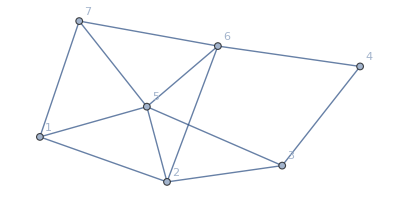

```mathematica
RandomGraph[{7,12},VertexLabels->Automatic]
```

```mathematica
VertexList[PetersenGraph[],_?(OddQ[VertexDegree[PetersenGraph[],#]]&)]
```

```mathematica
VertexList[-Graphics-,_?(OddQ[VertexDegree[-Graphics-,#]]&)]
```

{1,3,5,7}